#### ColorChecker资料： 2012年Bable的光谱测定： http://www.babelcolor.com/index_htm_files/ColorChecker_RGB_and_spectra.zip 第三方光谱测定：定量测定Classic与Passport的光谱分布区别： http://www.chromaxion.com/information/ColorChecker_Passport_Technical_Report.pdf 2014年染料改变后 观感对比： http://www.babelcolor.com/colorchecker-2.htm#xl_CCP2_beforeVSafter 官方软件提供的光谱数据（380nm-730nm interval 10nm）： Mac： ⁨Applications⁩ ▸ ⁨ColorChecker Camera Calibration⁩ ▸ ⁨Contents⁩ ▸ ⁨Resources⁩ ▸ ⁨Reference⁩ Win：\Program Files\X-Rite\ColorChecker Passport\win\Reference\ ColorChecker24_spectral.txt

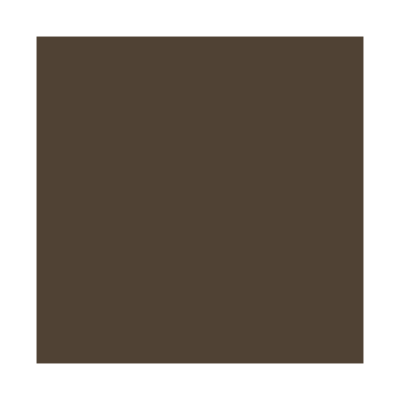
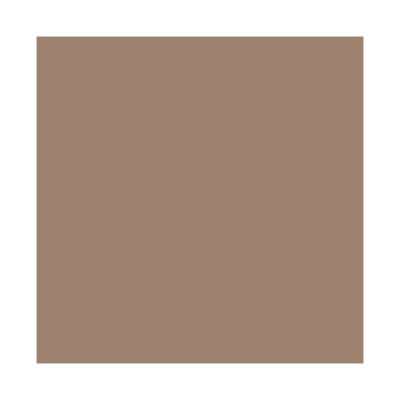
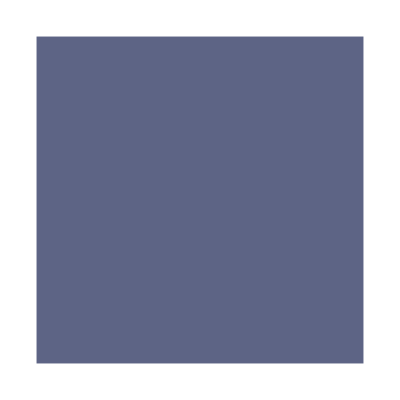
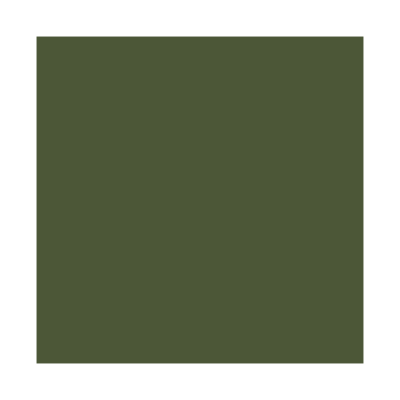
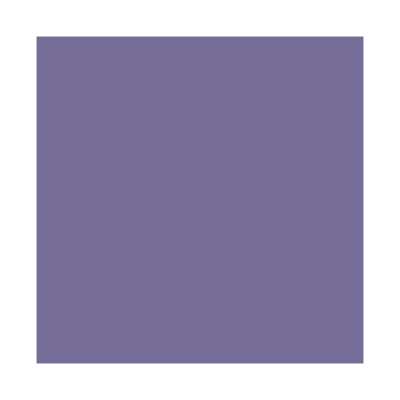
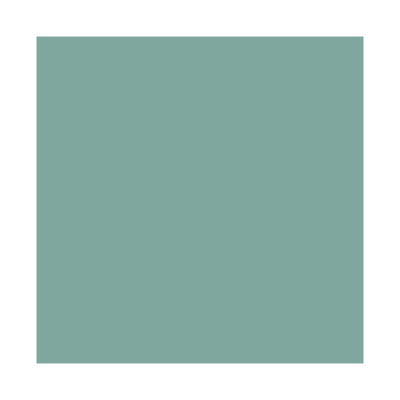
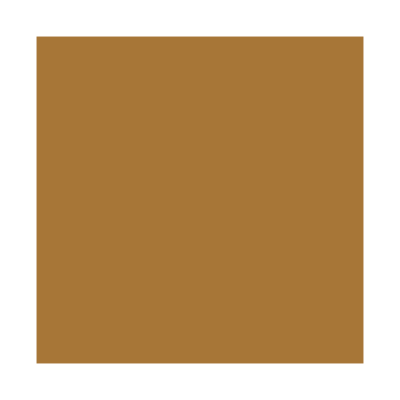
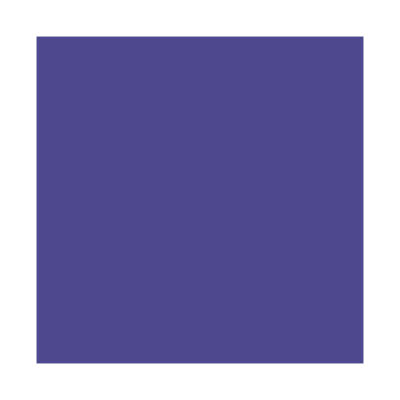
```mathematica
CC24A2014LAB=Import[gCSDir<>"/Data/ColorChecker/ColorChecker24_After_Nov2014Formatted.csv"];
CC24A2014XYZ=LAB2XYZ[#,"refWP"->"D50"]&/@CC24A2014LAB;

CC24Colors=RGBColor@(CM[#,
"iPri"->"XYZ",
"iWP"->"E",
"oPri"->"ProPhotoRGB",
"oWP"->"D50",
"Clip"->True
]~Power~(1/1.8))&/@CC24A2014XYZ
{RGBColor[{0.3155111163425482, 0.2581673853838577, 0.20547609813167342}],RGBColor[{0.6155806657179845, 0.5154070635076464, 0.4361687457564402}],RGBColor[{0.36597400476270303, 0.39106313043653373, 0.5204360104979568}],RGBColor[{0.29764426657090715, 0.34008902316100076, 0.21623689854129335}],RGBColor[{0.4634083797271608, 0.4310908933002799, 0.5992933958888506}],RGBColor[{0.499196976113721, 0.654408263451893, 0.6154934419008747}],RGBColor[{0.6541085776010427, 0.4636707673633955, 0.21373224686654543}],RGBColor[{0.30648990436731455, 0.2860168489383721, 0.5567248385856678}],RGBColor[{0.5483359025960951, 0.3195558294514752, 0.30509957624098577}],RGBColor[{0.2641633868868699, 0.19205661511573452, 0.31683430587663064}],RGBColor[{0.5548337830180871, 0.6561264229680344, 0.27978535050750203}],RGBColor[{0.7021741075986466, 0.5918133894061248, 0.23326066123868114}],RGBColor[{0.22223815977246514, 0.19263154806417887, 0.46482440796673097}],RGBColor[{0.3211494563502104, 0.4745051916799967, 0.2597416875880374}],RGBColor[{0.46692913808031783, 0.24028374743589012, 0.18269361967196296}],RGBColor[{0.7775773226237762, 0.7421123492584303, 0.25555558096883374}],RGBColor[{0.5517285527941359, 0.3184025409482046, 0.4814992940264946}],RGBColor[{0.28878250205943523, 0.4206531003655851, 0.5609027873642699}],RGBColor[{0.9285092083990454, 0.9332027006231239, 0.9082346725703854}],RGBColor[{0.7438502409372925, 0.7467359608017778, 0.7426471916094237}],RGBColor[{0.5685275539359577, 0.5721900248902292, 0.5715366337090473}],RGBColor[{0.39784126238108963, 0.39834000371623673, 0.39738942899077534}],RGBColor[{0.2582029398667287, 0.2599696043806236, 0.26179785804145306}],RGBColor[{0.14656210022990532, 0.14647061267666475, 0.14827934886067307}]}
Graphics[{#,Rectangle[]}]&/@CC24Colors
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
Partition[%,6];
ImageAssemble[%]
-Graphics-
```

```mathematica
(*图像导入*)
colorChecker=Import["ColorChecker-1.tif"][[1]];
colorCheckermask=Import["ColorCheckerMask.png"];
```

```mathematica
(*图像导入，调整大小，长边600，调整旋转*)
colorChecker600=ImageRotate[ImageResize[img,{600}],Pi]
```

-Graphics-

感谢https://mathematica.stackexchange.com/questions/45959/partitioning-an-image-based-on-features/45963

```mathematica
(*解析形态学分量*)
MorphologicalComponents@colorCheckermask;
(*选择面积大于1的分量，并编组*)
comps=SelectComponents[%,"Area",#>1&];
(*用“长方形外边框框住这些分量，即获得”*)
boundingBox=ComponentMeasurements[{comps,colorChecker600},"BoundingBox"];
patches=ImageTrim[colorChecker600,#]&/@boundingBox[[All,2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
patchesData=Mean@Flatten[ImageData[#],1]&/@Flatten[patches]
```

{{0.0943319,0.0677635,0.0569157},{0.237142,0.192158,0.177464},{0.120793,0.157548,0.198755},{0.0869348,0.102967,0.0682001},{0.161898,0.176383,0.226984},{0.184923,0.26607,0.259234},{0.24168,0.135335,0.0649638},{0.0866972,0.125982,0.20712},{0.207714,0.10207,0.103665},{0.0719826,0.0583461,0.0973196},{0.214082,0.240819,0.131548},{0.272068,0.196497,0.0887842},{0.0457797,0.0752935,0.150672},{0.105082,0.165691,0.108213},{0.168192,0.0574268,0.0467471},{0.264056,0.235049,0.109616},{0.211629,0.128104,0.178769},{0.102036,0.184803,0.228999},{0.359044,0.378598,0.382545},{0.280681,0.298766,0.305685},{0.208133,0.222991,0.227872},{0.132757,0.141743,0.144197},{0.0691334,0.0758052,0.0780474},{0.0282603,0.0303769,0.0311491}}

```mathematica
Draw1976XYZ[patchesData]
```

-Graphics3D-